```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&_∈Reals;
x1[theta_,z_]={rh*Cos[theta],rh*Sin[theta],z};
x0={rh,0,0};
dx[theta_,z_]=x1[theta,z]-x0;
rApx[theta_,z_]=dx[theta,z][[3]];
(*leading order*)StokesletsApx[theta_,z_]={{1/rApx[theta,z],0,0},{0,1/rApx[theta,z],0},{0,0,2/rApx[theta,z]}};
MatrixForm[StokesletsApx[theta,z]];
RotF[theta_]={{Cos[theta],-Sin[theta],0},{Sin[theta],Cos[theta],0},{0,0,1}};
MatrixForm[RotF[theta]];
SrotApx[z_]=Simplify[Integrate[StokesletsApx[theta,z].RotF[theta]*rh,{theta,0,2*Pi}]];
MatrixForm[SrotApx[z]]
MrotApx[z_]=2*Integrate[SrotApx[z],z];(*×2 becouse integrate over both sides.*)
MatrixForm[MrotApx[z]]
Mrot[z_]={{d11,0,0},{0,d22,0},{0,0,d33+MrotApx[z][[3,3]]}};
MatrixForm[Mrot[z]]
InvMrot[z_]=FullSimplify[Inverse[Mrot[z]]];
MatrixForm[InvMrot[z]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | (4 π rh)/z)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 8 π rh Log[z])

(d11 | 0 | 0
0 | d22 | 0
0 | 0 | d33+8 π rh Log[z])

(1/d11 | 0 | 0
0 | 1/d22 | 0
0 | 0 | 1/(d33+8 π rh Log[z]))

Inf cylinder inside inf cylinder, calculate force density.

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&_∈Reals;
zrh=rh/R;
f[rh_,R_]=FullSimplify[2*Pi*((1+4*Log[zrh])*zrh^4-(1-2*zrh^2)^2)/
((1-zrh^2) ((1-zrh^2)+(1+zrh^2)*Log[zrh]))];
f[rh,R]
FullSimplify[-(2 π (R^4))/((R^2)^2+(R^4) Log[rh/R])]
```

-(2 π (R^4-4 R^2 rh^2+3 rh^4+4 rh^4 Log[R/rh]))/((R^2-rh^2)^2+(R^4-rh^4) Log[rh/R])

-(2 π)/(1-Log[R]+Log[rh])

```mathematica
f[1,k*lh]
```

```mathematica
FullSimplify[-(2 π (k^4 lh^4))/((k^2 lh^2)^2+(k^4 lh^4) Log[1/(k lh)])]
```

-(2 π)/(1+Log[1/(k lh)])

```mathematica
Expand[Numerator[f[rh,R]/(2*Pi)]]
Expand[Denominator[f[rh,R]]]
```

-R^4+4 R^2 rh^2-3 rh^4-4 rh^4 Log[R/rh]

R^4-2 R^2 rh^2+rh^4+R^4 Log[rh/R]-rh^4 Log[rh/R]

-q1

-(2 π (R^4-4 R^2 rh^2+(3+4 q1) rh^4))/((R^2-rh^2)^2+R^4 Log[rh/R])

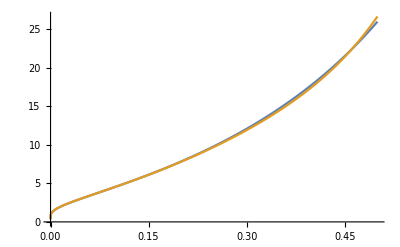

(-2*Pi*(R**4 - 4*R**2*rh**2 + (3 + 4*q1)*rh**4))/((R**2 - rh**2)**2 + R**4*Log(rh/R))

```mathematica
logApx=Normal[Series[Log[x],{x,Exp[-q1],0}]]
fapx[rh_,R_,q1_]=FullSimplify[(2 π (-R^4+4 R^2 rh^2-3 rh^4+4 rh^4 *logApx))/(R^4-2 R^2 rh^2+rh^4+R^4 Log[rh/R])];
fapx[rh,R,q1]
pw=PageWidth/.Options[$Output];
SetOptions[$Output,PageWidth->Infinity];
t1=fapx[rh,R,q1];
FortranForm[t1]
SetOptions[$Output,PageWidth->pw];
(*Plot[{f[rh,1],fapx[rh,1,1.464868309020669556730354088358581066131591796875]},{rh,0,0.5}]*)
Plot[{f[rh,1],fapx[rh,1,1.464868309020669556730354088358581066131591796875]},{rh,0,0.5}]
```

```mathematica
FullSimplify[fapx[rh,R,q1]]
FullSimplify[fapx[1,1/rh,q1]*rh]
FullSimplify[fapx[rh,1,q1]]
```

-(2 π (R^4-4 R^2 rh^2+(3+4 q1) rh^4))/((R^2-rh^2)^2+R^4 Log[rh/R])

-(2 π rh (1-4 rh^2+(3+4 q1) rh^4))/((-1+rh^2)^2+Log[rh])

-(2 π (1-4 rh^2+(3+4 q1) rh^4))/((-1+rh^2)^2+Log[rh])

```mathematica
Series[-(2 π (1-4 rh^2))/((-1+rh^2)^2+Log[rh]),{rh,0, 3}]
```

-(2 π)/(1+Log[rh])+(4 π (1+2 Log[rh]) rh^2)/(1+Log[rh])^2+O[rh]^4

```mathematica
FullSimplify[-(2 π (1-4 rh^2))/(1-2*rh^2+Log[rh])/.rh-> (rh/(kl*lh))]
```

-(2 π (1-(4 rh^2)/(kl^2 lh^2)))/(1-(2 rh^2)/(kl^2 lh^2)+Log[rh/(kl lh)])

Infinity cylinder inside inf cylinder, 2020 11 13.

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&_∈Reals;
zrh=rh/R;
f[rh_,R_]=FullSimplify[2*Pi*((1+4*Log[zrh])*zrh^4-(1-2*zrh^2)^2)/
((1-zrh^2) ((1-zrh^2)+(1+zrh^2)*Log[zrh]))];
f[rR,1]
```

-(2 π (1-4 rR^2+3 rR^4+4 rR^4 Log[1/rR]))/((1-rR^2)^2+(1-rR^4) Log[rR])

```mathematica
FullSimplify[Series[Numerator[f[rR,1]],{rR,0,3}]]
FullSimplify[Series[Denominator[f[rR,1]],{rR,0,3}]]
FullSimplify[Series[f[rR,1],{rR,0,3}]]
```

-2 π+8 π rR^2+O[rR]^4

(1+Log[rR])-2 rR^2+O[rR]^4

-(2 π)/(1+Log[rR])+(4 π (1+2 Log[rR]) rR^2)/(1+Log[rR])^2+O[rR]^4

```mathematica
f[rR,1]
Numerator[f[rR,1]]
Denominator[f[rR,1]]
```

-(2 π (1-4 rR^2+3 rR^4+4 rR^4 Log[1/rR]))/((1-rR^2)^2+(1-rR^4) Log[rR])

-2 π (1-4 rR^2+3 rR^4+4 rR^4 Log[1/rR])

(1-rR^2)^2+(1-rR^4) Log[rR]

slop of alpha_max line

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&ahinf>0&&atinf>0&&kappa>0&&n1>0&&n1>0&&rh∈Reals&&ahinf∈Reals&&atinf∈Reals&&kappa∈Reals&&n1∈Reals&&dah∈Reals;
alpha=FullSimplify[(ahinf  * (lh/Log[lh/rh])/ (n1/Log[n1])+atinf)/((ahinf+dah*(rh/lh)^2)* lh/n1+at)];
alpha=FullSimplify[(ahinf  * (lh/Log[lh/rh])/ (n1/Log[n1]))/((ahinf+dah*(rh/lh)^2)* lh/n1+at)];
(*alpha=FullSimplify[(ahinf * rh * (kappa/Log[kappa])/ (n1/Log[n1])+atinf)/((ahinf+dah*rh^2)* rh * kappa/n1)];*)
(*alpha=FullSimplify[(ahinf * rh * (kappa/Log[kappa])/ (n1/Log[n1]))/((ahinf+dah*rh)* rh * kappa/n1+atinf+dat)]*)
alpha=(ahinf * rh * kappa/n1)/((ahinf+dah*(1/kappa)^2)* rh * kappa/n1+at)
(*alpha=(ahinf * rh * kappa/n1+atinf)/((ahinf+dah*rh^2)* rh * kappa/n1);*)
(*alpha=(ahinf * rh * kappa/n1)/((ahinf+dah*rh^2)* rh * kappa/n1+at);*)
(*alpha=(ahinf * rh * kappa/n1+atinf)/((ahinf+dah*rh^2)* rh * kappa/n1+atinf+dat)*)
FullSimplify[D[alpha,rh]]
FullSimplify[D[alpha,n1]]
(*FullSimplify[Solve[Numerator[FullSimplify[D[alpha,rh]]]==0,rh]]*)
```

(ahinf kappa rh)/(n1 (at+((ahinf+dah/kappa^2) kappa rh)/n1))

(ahinf at kappa^3 n1)/((at kappa n1+(dah+ahinf kappa^2) rh)^2)

-(ahinf at kappa^3 rh)/((at kappa n1+(dah+ahinf kappa^2) rh)^2)

```mathematica
alpha=FullSimplify[(ahinf * rh * (kappa/Log[kappa])*Log[n1])/(ahinf* rh * kappa+2*at*n1)]
FullSimplify[D[alpha,n1]]
```

(ahinf kappa rh Log[n1])/(2 at n1 Log[kappa]+ahinf kappa rh Log[kappa])

(ahinf kappa rh (2 at n1+ahinf kappa rh-2 at n1 Log[n1]))/(n1 (2 at n1+ahinf kappa rh)^2 Log[kappa])

### 20201126 version, apply kappa = lh / rh

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&ahinf>0&&atinf>0&&kappa>0&&n1>0&&n1>0&&rh∈Reals&&ahinf∈Reals&&atinf∈Reals&&kappa∈Reals&&n1∈Reals&&dah∈Reals;
alpha=(ahinf * (rh * kappa/lt)*(Log[kappa]/Log[lt/rt]))/((ahinf+dah* rh^2)* (rh *kappa/lt)+at)
(*alpha=(ahinf * rh * kappa/lt+atinf)/((ahinf+dah /kappa^2)* rh * kappa /lt+at)*)
FullSimplify[D[alpha,rh]]
FullSimplify[D[alpha,lt]]
```

(ahinf kappa rh Log[kappa])/(lt (at+(kappa rh (ahinf+dah rh^2))/lt) Log[lt/rt])

(ahinf kappa (at lt-2 dah kappa rh^3) Log[kappa])/((at lt+kappa rh (ahinf+dah rh^2))^2 Log[lt/rt])

-(ahinf kappa rh Log[kappa] (at lt+kappa rh (ahinf+dah rh^2)+at lt Log[lt/rt]))/(lt (at lt+kappa rh (ahinf+dah rh^2))^2 Log[lt/rt]^2)

### 20201215 version, Taylor series of = lh / lt

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&ahinf>0&&atinf>0&&kappa>0&&n1>0&&n1>0&&rh∈Reals&&ahinf∈Reals&&atinf∈Reals&&kappa∈Reals&&n1∈Reals&&dah∈Reals;
alpha=(ahinf * lhlt*Log[lt]/Log[lh]+atinf)/(ah* lhlt+at)
Series[alpha,{lhlt,0,1}]
```

(atinf+(ahinf lhlt Log[lt])/Log[lh])/(at+ah lhlt)

atinf/at+(-(ah atinf)/at^2+(ahinf Log[lt])/(at Log[lh])) lhlt+O[lhlt]^2

### 20210205 version

```mathematica
Clear["Global`*"]
$Assumptions=rh>0&&lh>0&&ahinf>0&&at>0&&rt>0&&lt>0&&rh∈Reals&&lh∈Reals&&ahinf∈Reals&&at∈Reals&&rt∈Reals&&lt∈Reals;
alpha=2*Pi /(2*Pi/Log[R/rh]+at* lt/lh)*(Log[lt/rt]/Log[lh/rh])
lt = Solve[FullSimplify[D[alpha,lt]]==0,lt][[1]][[1]][[2]]
FullSimplify[alpha];
FullSimplify[D[FullSimplify[alpha],lh]]
lh = Solve[FullSimplify[D[FullSimplify[alpha],lh]]==0,lh][[1]][[1]][[2]]
FullSimplify[alpha]
```

(2 π Log[lt/rt])/(Log[lh/rh] ((at lt)/lh+(2 π)/Log[R/rh]))

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(2 lh π)/(at Log[R/rh] ProductLog[(2 lh π)/(at ⅇ rt Log[R/rh])])

-(Log[R/rh] ProductLog[(2 lh π)/(at ⅇ rt Log[R]-at ⅇ rt Log[rh])] (1-Log[lh]+Log[rh]+ProductLog[(2 lh π)/(at ⅇ rt Log[R]-at ⅇ rt Log[rh])]))/(lh Log[lh/rh]^2 (1+ProductLog[(2 lh π)/(at ⅇ rt Log[R]-at ⅇ rt Log[rh])]))

ⅇ^((2 π rh+at rt Log[R]-at rt Log[rh]+at rt Log[R] Log[rh]-at rt Log[rh]^2)/(at rt (Log[R]-Log[rh])))

(Log[ⅇ^(1+ProductLog[(2 ⅇ^((2 π rh)/(at rt Log[R]-at rt Log[rh])) π rh)/(at rt Log[R]-at rt Log[rh])])] Log[R/rh] ProductLog[(2 ⅇ^((2 π rh)/(at rt Log[R]-at rt Log[rh])) π rh)/(at rt Log[R]-at rt Log[rh])])/(Log[ⅇ^(1+(2 π rh)/(at rt Log[R]-at rt Log[rh]))] (1+ProductLog[(2 ⅇ^((2 π rh)/(at rt Log[R]-at rt Log[rh])) π rh)/(at rt Log[R]-at rt Log[rh])]))

```mathematica
ⅇ rt Log[R] / Exp[1]
```

rt Log[R]

```mathematica
Solve[lh^(1-a1)==Log[lh],a1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a1→(Log[lh]-Log[Log[lh]])/Log[lh]}}